```mathematica
Assuming[amax>0,Integrate[PDF[NormalDistribution[μ,σ],x]PDF[UniformDistribution[{0,amax}],σ],{σ,0,amax}]]
```

Piecewise[{{Gamma[0,(x-μ)^2/(2 amax^2)]/(2 amax √(2 π)), amax>0&&Re[(x-μ)^2]≥0}, {Integrate[(ⅇ^(-(x-μ)^2/(2 σ^2)) (Piecewise[{{1/amax, 0≤σ≤amax}, {0, True}}]))/(√(2 π) σ),{σ,0,amax},Assumptions→Re[(x-μ)^2]<0&&amax>0], True}}]

```mathematica
Assuming[{b>0,n>0,sse>0},Integrate[(1/(Sqrt[2 π σ^2]))^n Exp[-sse/(2 σ^2)] PDF[UniformDistribution[{0,b}],σ],{σ,0,b}]]
```

2^(-1-n/2) b^-n π^(-n/2) ExpIntegralE[3/2-n/2,sse/(2 b^2)]

```mathematica
ExpIntegralE
```

```mathematica
Simplify@Log[2^(-1-n/2) b^-n π^(-n/2) ExpIntegralE[3/2-n/2,sse/(2 b^2)]]
```

Log[2^(-1-n/2) b^-n π^(-n/2) ExpIntegralE[3/2-n/2,sse/(2 b^2)]]

```mathematica
N@ExpIntegralE[1,30]
```

3.02155×10^-15

```mathematica
FunctionExpand[2^(-1-n/2) amax^-n π^(-n/2) ExpIntegralE[3/2-n/2,sse/(2 amax^2)]]
```

(amax^-n π^(-n/2) (sse/amax^2)^(1/2-n/2) Gamma[-1/2+n/2,sse/(2 amax^2)])/(2 √2)

```mathematica
Assuming[{a>0,b>0},FullSimplify@Log@ExpIntegralE[a,b]]
```

Log[ExpIntegralE[a,b]]

```mathematica
N@ExpIntegralE[-48.5,1]
```

8.6676×10^61

```mathematica
N@ExpIntegralE[1.2,2]
```

0.0461834+8.24546×10^-16 ⅈ

```mathematica
ExpIntegralE[-48.5,0.45]
```

1.27022×10^79

```mathematica
N@ExpIntegralE[1,2]
```

0.0489005

```mathematica
N@Gamma[3,2]
```

1.35335

```mathematica
Gamma[2]-
```

1

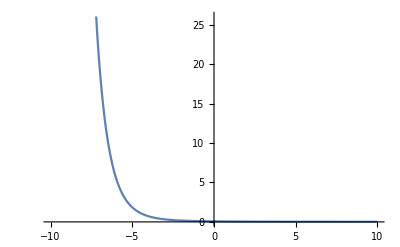

```mathematica
Plot[Re@ExpIntegralE[x,2],{x,-10,10}]
```

```mathematica
Plot[ExpIntegralE[2,2]
```

## Try out with simple N(μ,σ) model

```mathematica
x = RandomVariate[NormalDistribution[5, 7],10];
```

```mathematica
fPrior[μ_,σ_,amax_]:=PDF[NormalDistribution[10,5],μ] PDF[UniformDistribution[{0,amax}],σ]
fLikelihood[x__,μ_,σ_]:=Likelihood[NormalDistribution[μ,σ],x]
```

```mathematica
aint=NIntegrate[fLikelihood[x,μ,σ] fPrior[μ,σ,100],{μ,0,∞},{σ,0,100}]
```

1.13834×10^-17

```mathematica
fPosterior[μ_,σ_,x__,amax_,aint_]:=fLikelihood[x,μ,σ] fPrior[μ,σ,amax]/aint
```

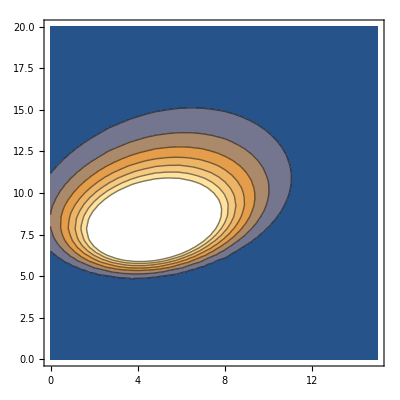

```mathematica
ContourPlot[fPosterior[μ,σ,x,100,aint],{μ,0,15},{σ,0,20}]
```

```mathematica
fMarginalPosterior[μ_,x__,amax_,aint_]:=NIntegrate[fPosterior[μ,σ,x,amax,aint],{σ,0,amax}]
```

```mathematica
NIntegrate[μ fPosterior[μ,σ,x,100,aint],{μ,0,∞},{σ,0,100}]
```

5.18893

```mathematica
NIntegrate[μ fMarginalPosterior[μ,x,100,aint],{μ,0,∞}]
```

NormalDistribution::realprm: Parameter ∞ at position 1 in NormalDistribution[∞,σ] is expected to be real.

NIntegrate::inumr: The integrand 8.78474×10^16 Likelihood[NormalDistribution[∞,σ],{5.37698,4.61535,15.2442,4.07848,1.69595,-1.44081,-12.8902,-3.80279,7.96539,12.0238}] PDF[NormalDistribution[10,5],∞] (Piecewise[{{1/100, 0≤σ≤100}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

NormalDistribution::realprm: Parameter ∞ at position 1 in NormalDistribution[∞,σ] is expected to be real.

NIntegrate::inumr: The integrand 8.78474×10^16 Likelihood[NormalDistribution[∞,σ],{5.37698,4.61535,15.2442,4.07848,1.69595,-1.44081,-12.8902,-3.80279,7.96539,12.0238}] PDF[NormalDistribution[10,5],∞] (Piecewise[{{1/100, 0≤σ≤100}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

NormalDistribution::realprm: Parameter ∞ at position 1 in NormalDistribution[∞,σ] is expected to be real.

General::stop: Further output of NormalDistribution::realprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand 8.78474×10^16 Likelihood[NormalDistribution[∞,σ],{5.37698,4.61535,15.2442,4.07848,1.69595,-1.44081,-12.8902,-3.80279,7.96539,12.0238}] PDF[NormalDistribution[10,5],∞] (Piecewise[{{1/100, 0≤σ≤100}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

5.18893

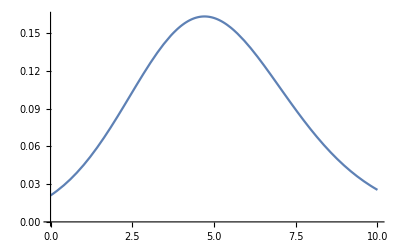

```mathematica
Plot[fMarginalPosterior[μ,x,100,aint],{μ,0,10}]
```

### Now with integrated out method

```mathematica
fMarginalPosterior1[μ_,x__,b_,aint_]:=Block[{sse=Total[(x-μ)^2],n=Length@x},(2^(-1-n/2) b^-n π^(-n/2) ExpIntegralE[3/2-n/2,sse/(2 b^2)]/aint) PDF[NormalDistribution[10,5],μ] ]
```

```mathematica
Plot[fMarginalPosterior1[μ,x,100,aint],{μ,0,10}]
```

-Graphics-

```mathematica
NIntegrate[fMarginalPosterior1[μ,x,100,aint],{μ,0,100}]
```

1.

## Try other priors

### Gamma

```mathematica
Assuming[{a>0,b>0,sse>0},Integrate[(1/(Sqrt[2 π σ^2]))^n Exp[-sse/(2 σ^2)] PDF[GammaDistribution[a,b],σ],{σ,0,∞}]]
```

```mathematica
FullSimplify[1/Gamma[a] 2^(-3/2-a/2-n/2) b^(-1-a-n) π^(-n/2) sse^(-n/2) (2^(1/2+n/2) b^(1+n) sse^(a/2) Gamma[1/2 (-a+n)] HypergeometricPFQ[{},{1/2,1+a/2-n/2},-sse/(8 b^2)]-2^(n/2) b^n sse^(1/2+a/2) Gamma[1/2 (-1-a+n)] HypergeometricPFQ[{},{3/2,3/2+a/2-n/2},-sse/(8 b^2)]+2^(3/2+a/2) b^(1+a) sse^(n/2) Gamma[a-n] HypergeometricPFQ[{},{1/2-a/2+n/2,1-a/2+n/2},-sse/(8 b^2)])]
```

1/Gamma[a]2^(1/2 (-5-a-3 n)) b^(-1-a-n) π^(3/2-n/2) sse^(-n/2) (-2^((3 (1+n))/2) b^(1+n) sse^(a/2) Csc[1/2 (a-n) π] HypergeometricPFQRegularized[{},{1/2,1/2 (2+a-n)},-sse/(8 b^2)]+2^(5/2+(3 a)/2) b^(1+a) sse^(n/2) Csc[(a-n) π] HypergeometricPFQRegularized[{},{1/2 (1-a+n),1/2 (2-a+n)},-sse/(8 b^2)]+2^(3 n/2) b^n sse^((1+a)/2) HypergeometricPFQRegularized[{},{3/2,1/2 (3+a-n)},-sse/(8 b^2)] Sec[1/2 (a-n) π])

### Inverse gamma

```mathematica
Assuming[{a>0,b>0,sse>0,n>0},Integrate[(1/(Sqrt[2 π σ^2]))^n Exp[-sse/(2 σ^2)] PDF[InverseGammaDistribution[a,b],σ],{σ,0,∞}]]
```

(2^(-a/2-n) b^a π^(-n/2) sse^(-a/2-n/2) Gamma[a+n] HypergeometricU[(a+n)/2,1/2,b^2/(2 sse)])/Gamma[a]

### Normal

```mathematica
Assuming[{a>0,b>0,sse>0,n>0},Integrate[(1/(Sqrt[2 π σ^2]))^n Exp[-sse/(2 σ^2)] PDF[NormalDistribution[a,b],σ],{σ,0,∞}]]
```

∫_0^∞ (ⅇ^(-sse/(2 σ^2)-(-a+σ)^2/(2 b^2)) (2 π)^(-1/2-n/2) (σ^2)^(-n/2))/b ⅆσ

### Student t

```mathematica
Assuming[{a>0,b>0,sse>0,n>0,c>0},Integrate[(1/(Sqrt[2 π σ^2]))^n Exp[-sse/(2 σ^2)] PDF[StudentTDistribution[a,b,c],σ],{σ,0,∞}]]
```

∫_0^∞ (ⅇ^(-sse/(2 σ^2)) (2 π)^(-n/2) (σ^2)^(-n/2) (c/(c+(-a+σ)^2/b^2))^((1+c)/2))/(b √c Beta[c/2,1/2])ⅆσ